## Relu and Softmax Graphs

```mathematica
ClearAll["Global`*"]
```

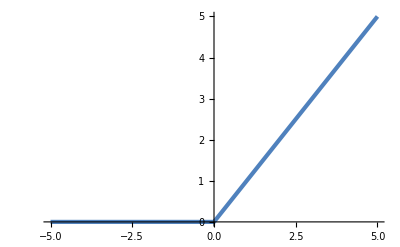

```mathematica
relu[t_]=Piecewise[{{0, t<0},{t,t>0}}];
p1=Plot[relu[t],{t,-5,5}, PlotStyle->Directive[RGBColor[0.3098,0.50588,0.74117], AbsoluteThickness[3]]]
```

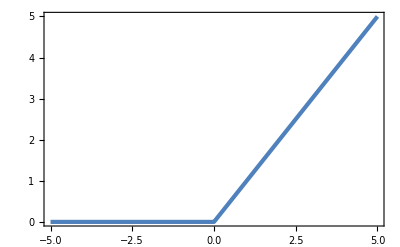
-Graphics-Relu Activation Function

```mathematica
s1=Labeled[Show[p1, Frame->True, AxesStyle->Directive[Black, Bold], FrameStyle->Directive[Black,Bold]],"Relu Activation Function" ,{Top}, LabelStyle->Directive[Black, Bold]]
```

```mathematica
Export[NotebookDirectory[]<>"relu.png", s1,ImageResolution->100]
```

C:\Users\Ian\AppData\Local\Programs\Python\Python35\Scripts\Face_recognition\relu.png

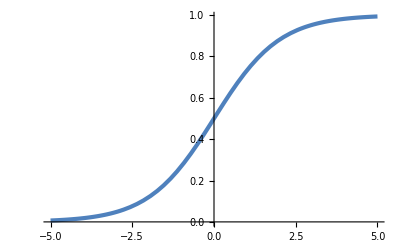

```mathematica
soft[t_]=1/(1+ⅇ^-t);
p2=Plot[soft[t],{t,-5,5},PlotStyle->Directive[RGBColor[0.3098,0.50588,0.74117], AbsoluteThickness[3]]]
```

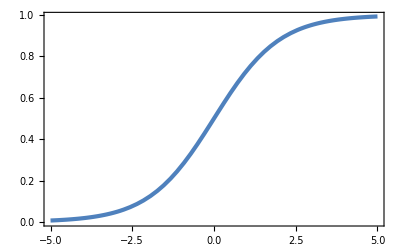
-Graphics-Softmax Activation Function

```mathematica
s2=Labeled[Show[p2, Frame->True, AxesStyle->Directive[Black, Bold], FrameStyle->Directive[Black,Bold]],"Softmax Activation Function" ,{Top}, LabelStyle->Directive[Black, Bold]]
```

```mathematica
Export[NotebookDirectory[]<>"soft.png", s2,ImageResolution->100]
```

C:\Users\Ian\AppData\Local\Programs\Python\Python35\Scripts\Face_recognition\soft.png